```mathematica
Clear[MD,MD2,i,j,k,pop,d,w,popWyst,wystepowanie,osobnik,pbilMD,generateNew]
```

Max diversity
Z=∑_(i=1)^(n-1) ∑_(j=i+1)^n d_ij x_ix_j, gdzie dodatkowo ∑_(i=1)^n x_i=m, d_ij= (∑_(k=1)^r (s_ik-s_jk)^2)^(1/2)

```mathematica
d[i_,j_,X_]:=√(∑_(k=1)^Length[X⟦i⟧] (X⟦i,k⟧-X⟦j,k⟧)^2);(*Odległość i-tego od j-tego wektora ze zbioru X*)
(*X-wszystkie osobniki,xWyst - konkretny osobnik, w którym wartość liczymy (jako osobnik-wystepowanie)*)
MD[X_,xWyst_]:=∑_(ix=1)^(Length[xWyst]-1) ∑_(jx=ix+1)^Length[xWyst] d[ix,jx,X] xWyst⟦ix⟧ xWyst⟦jx⟧;
MD2[X_,pop_]:=Module[{wyst},(*Operuje na podzbiorach*)
em=Length[pop];
en=Length[X];
wyst=Table[0,{en}];
For[ix=1,ix≤em,ix++,
For[jx=1,jx≤en,jx++,
If[pop⟦ix⟧==X⟦jx⟧,wyst⟦jx⟧=1]
]];
MD[X,wyst]
]
```

SetDelayed::write: Tag Real in 3.6199824615003381×10^9[i_, j_, X_] is Protected.

```mathematica
MD[t1,w]
```

2+√2

```mathematica
MD2[t1,{{1,0,1},{1,1,1},{0,1,1}}]
```

m: 3

n: 4

{0,0,0,0}

0

```mathematica
t1={{1,0,1},{0,0,1},{1,1,1},{0,1,1}}(*Wektos testowy*)
```

{{1,0,1},{0,0,1},{1,1,1},{0,1,1}}

```mathematica
d[2,3,t1]
```

√2

```mathematica
SeedRandom[11];
t2=Table[RandomInteger[],{nPop,1,10},{dl,1,3}]
(* n el. tablica dana *)
```

{{0,0,1},{1,0,1},{1,1,1},{0,1,1},{1,1,0},{1,1,1},{0,1,0},{0,1,1},{0,0,1},{0,0,0}}

```mathematica
d[1,5,t2]
```

√3

```mathematica
w={1,0,1,1}
```

{1,0,1,1}

```mathematica
(*Wybór m-elementowego podzbioru poprzez wypisanie wektora 0/1 *)
wystepowanie[tab_,em_]:=Module[
{t=tab,en,ksi,wyn},
en=Length[t];
ksi=RandomSample[Range[en],em];
wyn=Table[0,{en}];
For[ix=1,ix≤em,ix++,
wyn⟦ksi⟦ix⟧⟧=1];
Return[wyn]
]
(*Wyznacza populację na podstawie występowania*)
popWyst[wyst_,tab_]:=Module[{en,em,pop},
en=Length[tab];(*wielkość populacji*)
em=valuate[wyst];(*il. wybranych el*)
pop=Table[tab⟦1⟧,{em}];
jx=1;
For[ix=1,ix≤en,ix++,
If[wyst⟦ix⟧==1,pop⟦jx⟧=tab⟦ix⟧;jx++]];
Return[pop]
];
(*wyznacza występowanie na podstawie populacji*)
wystPop[pop_,tab_]:=Module[{n,m,wyst},
n=Length[tab];
m=Length[pop];
wyst=Table[0,{n}];
For[i=1,i≤n,i++,
For[j=1,j≤m,j++,
If[tab⟦i⟧==pop⟦j⟧,wyst⟦i⟧=1]]];
Return [wyst]
]
```

```mathematica
t2
```

{{0,0,1},{1,0,1},{1,1,1},{0,1,1},{1,1,0},{1,1,1},{0,1,0},{0,1,1},{0,0,1},{0,0,0}}

```mathematica
w=wystepowanie[t2,3]
(* tablica określająca, który el. tab. t2 należy do podzbioru *)
```

{0,0,0,1,0,1,0,0,0,1}

```mathematica
popul=popWyst[w,t2]
```

{{0,1,1},{1,1,1},{0,0,0}}

```mathematica
MD[t2,w]
```

1+√2+√3

## PBIL 3 (dla max diversity)

```mathematica
(*Losuje osobnika długości n z m jedynkami*)
valuate[x_]:=Module[{},∑_(i=1)^Length[x] x⟦i⟧];
osobnik[p_,n_,m_]:=Module[{x=Table[0,{n}]},
SeedRandom[];
While[valuate[x]!=m, 
For[i=1,i<=n,i++,
x⟦i⟧=RandomChoice[{p,1-p}->{0,1}];
];
];x
];
```

```mathematica
(*generowanie nowego osobnika kolejnej populacji*)
generateNew[P_,n_,m_,X_]:=Module[{newPopulWyst,newPopul,tmp},
SeedRandom[];
newPopulWyst=Table[0,{n}];
tmp=RandomSample[P->Range[n],m];(*wylosowanie m współrzędnych z n z prawdop P[[i]]*)
For[i=1,i<=m,i++,
newPopulWyst⟦tmp⟦i⟧⟧=1];
newPopul=popWyst[newPopulWyst,X ]
];
compare[x_,y_,X_]:=Module[{},
If[MD2[x,X]>MD2[y,X],x,y]];(*porownanie odległość podzbioru x od X z odległością podzbioru y od X*)
```

```mathematica
Xx={{0,0,0},{1,12,2},{2,1,5}};
generateNew[{0.4,0.1,0.9},3,2,Xx]
```

{{0,0,0},{2,1,5}}

```mathematica
osobnik[0.5,3,2]
```

{0,1,1}

```mathematica
valuate[w]
```

3

```mathematica
(*X-zbiór wektorów, λ-współczynnik uczenia się, m-ile osobników wybieramy,size-wielkość populacji,max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm*)

pbilMD[X_,λ_,m_,size_,max_,itmax_]:=Module[{P,best, iter=1,wynik=Table[{0,0},{1}],n},
(*generacja pop startowej*)
SeedRandom[];
n=Length[X]; (*wielkośc bazy*)
P=Table[0.5,{n}];
(*Zainicjowanie populacji*)
population=Table[0,{size}];
For[k=1,k<=size,k++,
population⟦k⟧=popWyst[wystepowanie[X,m],X]];(*Losowy podzbiór X jako osobnik startowej populacji*)
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
Print["P: ",P];
(*Algorytm kończy działanie po ustalonej ilości iteracji*)
While[(MD2[X,best]≠max  && iter≠itmax),
(*wyszukiwanie najlepszego osobnika*)
For[k=1,k≤size,k++,
best=compare[population⟦k⟧,best,X]];
wynik⟦iter⟧={iter,MD2[best,X]};
(*Obliczenie nowego wektora prawdopodobienstwa*)
For[k=1,k<=n,k++,
P⟦k⟧=(1-λ) P⟦k⟧+λ *(wystPop[best,X]⟦k⟧)];

(*Generacja nowej populacji*)
For[k=1,k<=size,k++,
population⟦k⟧=generateNew[P,n,m,X]];

iter++;
wynik2=Table[{iter,MD2[best,X]},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];
Print["Maximum = ",MD2[best,X]," (rzeczywiste = ",max,") uzyskane po iteracjach: ",iter-1," dla punktów: "];
Print[best];
(*Print[wynik];*)
(*If[Length[X⟦1⟧]==2,
Show[ListPlot[X,PlotStyle->Directive[PointSize[Medium],Purple]],ListPlot[best,PlotStyle->Directive[PointSize[0.02],Red]]],
If[Length[X⟦1⟧]==3,
Show[ListPointPlot3D[X,PlotStyle->{PointSize[Medium],Blue}],ListPointPlot3D[best,PlotStyle->Directive[PointSize[0.02],Red]]]]
]*)
(*ListLinePlot[wynik]*)
]
```

TESTY

```mathematica
q=wystepowanie[t1,2]
```

{1,0,1,0}

```mathematica
popWyst[wystepowanie[t1,3],t1]
```

{{0,1},{1,0},{1,1}}

```mathematica
popWyst[q,t1]
```

{{0,0},{1,0}}

P: {0.5,0.5,0.5,0.5}

Maximum = √2 (rzeczywiste = √2) uzyskane po iteracjach: 9

{{0,0},{1,1}}

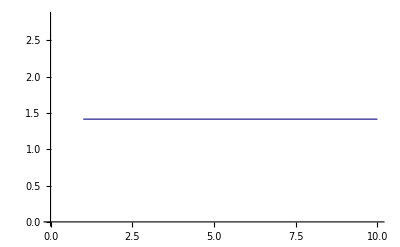

```mathematica
t1={{0,0},{0,1},{1,0},{1,1}};(*X,λ,m,size,max, iter*)
pbilMD[t1,0.01,2,4,Sqrt[2],10]
```

P: {0.5,0.5,0.5,0.5,0.5}

Maximum = 4+2 √2 (rzeczywiste = 2+2 √5) uzyskane po iteracjach: 9

{{0,0},{0,2},{2,2}}

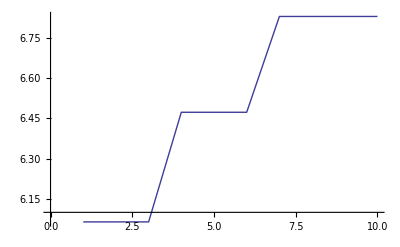

```mathematica
t2={{0,0},{0,1},{0,2},{1,0},{2,2}};(*X,λ,m,size,max, iter*)
pbilMD[t2,0.01,3,4,2+2*Sqrt[5],10]
```

Wierzchołki kwadratu (m=3)

P: {0.5,0.5,0.5,0.5}

Maximum = 2+√2 (rzeczywiste = 2+√2) uzyskane po iteracjach: 0 dla punktów:

{{0,0},{1,0},{1,1}}

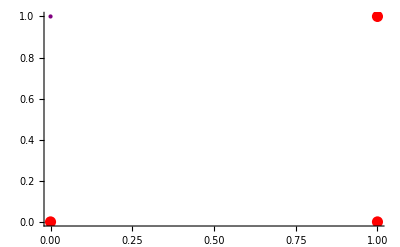

```mathematica
t3={{0,0},{0,1},{1,0},{1,1}};(*X,λ,m,size,max, iter*)
pbilMD[t3,0.01,3,4,2+Sqrt[2],10]
```

Wierzchołki kwadratu (m=2)

P: {0.5,0.5,0.5,0.5}

Maximum = √2 (rzeczywiste = √2) uzyskane po iteracjach: 0 dla punktów:

{{0,0},{1,1}}

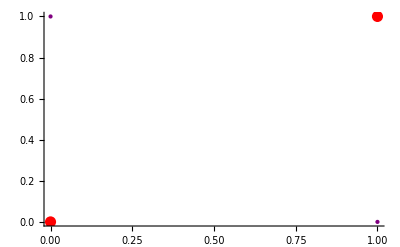

```mathematica
t3={{0,0},{0,1},{1,0},{1,1}};
(*X,λ,m,size,max, iter*)
pbilMD[t3,0.01,2,4,Sqrt[2],10]
```

Sześcian

```mathematica
t3={{0,0,0},{0,0,1},{0,1,0},{1,0,0},{1,1,0},{1,0,1},{0,1,1},{1,1,1}};(*X,λ,m,size,max, iter*)
max=Sqrt[3]+2Sqrt[2];
pbilMD[t3,0.01,3,4,max,15]
```

P: {0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

Maximum = 3 √2 (rzeczywiste = 2 √2+√3) uzyskane po iteracjach: 14 dla punktów:

{{1,1,0},{1,0,1},{0,1,1}}

TESTY AUTOMATIC

```mathematica
(*X-zbiór wektorów, λ-współczynnik uczenia się, m-ile osobników wybieramy,size-wielkość populacji,max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm*)

pbilMDtest[X_,λ_,m_,size_,max_,itmax_]:=Module[
{P,best, iter=1,wynik=Table[{0,0},{1}],n,nmax=max},
(*generacja pop startowej*)
SeedRandom[];
n=Length[X]; (*wielkośc bazy*)
P=Table[0.5,{n}];
(*Zainicjowanie populacji*)
population=Table[0,{size}];
For[k=1,k<=size,k++,
population⟦k⟧=popWyst[wystepowanie[X,m],X]];(*Losowy podzbiór X jako osobnik startowej populacji*)
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
(*Algorytm kończy działanie po ustalonej ilości iteracji*)
While[(MD2[X,best]≠nmax  && iter≠itmax),
If[MD2[X,best]>nmax,nmax=MD2[X,best]];
(*wyszukiwanie najlepszego osobnika*)
For[k=1,k≤size,k++,
best=compare[population⟦k⟧,best,X]];

(*Obliczenie nowego wektora prawdopodobienstwa*)
For[k=1,k<=n,k++,
P⟦k⟧=(1-λ) P⟦k⟧+λ *(wystPop[best,X]⟦k⟧)];

(*Generacja nowej populacji*)
For[k=1,k<=size,k++,
population⟦k⟧=generateNew[P,n,m,X]];

iter++;
wynik2=Table[{iter,MD2[X,best]},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];
(*Znalazł/nie maksimum zadane*)
If[MD2[X,best]==nmax,Return[{1,iter,nmax}],Return[{0,iter,nmax}]]


]
```

KWADRAT (m=3)

```mathematica
t3={{0,0},{0,1},{1,0},{1,1}};(*X,λ,m,size,max, iter*)
pbilMDtest[t3,0.01,3,4,2+Sqrt[2],10]
```

{1,1,2+√2}

```mathematica
λ={.5,.2,.1,.01,.0001};
mm=3;size={3,5,20,50,100};max=2+Sqrt[2];iter=100;X=t3;

For[ii=1,ii<=Length[λ],ii++,
For[jj=1,jj<=Length[size],jj++,
wyn={0,0}; it=0;perc=0;
For[q=1,q<=100,q++,
wyn=pbilMDtest[X,λ⟦ii⟧,mm,size⟦jj⟧,max,iter];
it+=wyn⟦2⟧;
perc+=wyn⟦1⟧];
Print["λ = ",λ[[ii]],", size = ",size[[jj]], " it = ",it/100.,", % : ",perc, " (max: ",If[wyn[[3]]>max,
wyn[[3]],max],")"];

];
Print["______________________"]
]
```

λ = 0.5, size = 3 it = 1., % : 100 (max: 2+√2)

λ = 0.5, size = 5 it = 1., % : 100 (max: 2+√2)

λ = 0.5, size = 20 it = 1., % : 100 (max: 2+√2)

λ = 0.5, size = 50 it = 1., % : 100 (max: 2+√2)

λ = 0.5, size = 100 it = 1., % : 100 (max: 2+√2)

______________________

λ = 0.2, size = 3 it = 1., % : 100 (max: 2+√2)

λ = 0.2, size = 5 it = 1., % : 100 (max: 2+√2)

λ = 0.2, size = 20 it = 1., % : 100 (max: 2+√2)

λ = 0.2, size = 50 it = 1., % : 100 (max: 2+√2)

λ = 0.2, size = 100 it = 1., % : 100 (max: 2+√2)

______________________

λ = 0.1, size = 3 it = 1., % : 100 (max: 2+√2)

λ = 0.1, size = 5 it = 1., % : 100 (max: 2+√2)

λ = 0.1, size = 20 it = 1., % : 100 (max: 2+√2)

λ = 0.1, size = 50 it = 1., % : 100 (max: 2+√2)

λ = 0.1, size = 100 it = 1., % : 100 (max: 2+√2)

______________________

λ = 0.01, size = 3 it = 1., % : 100 (max: 2+√2)

λ = 0.01, size = 5 it = 1., % : 100 (max: 2+√2)

λ = 0.01, size = 20 it = 1., % : 100 (max: 2+√2)

$Aborted

GENEROWANIE LOSOWYCH PKT KULI

```mathematica
SeedRandom[31546];pkty=Table[{0,0},{10}];
i=1;
While[i≠7,
pkty[[i++,1]]=Random[Real,{-1,1}]
];pkty
```

```mathematica
pkty={{0.5,-0.5},{0.4,0.1},{-0.9,-0.1},{0.1,0.12},{-.32,.14},{-0.1,0.58},{.911,.2},{-.77,.58},{0.14,-.85},{-.14,-.13}};
```

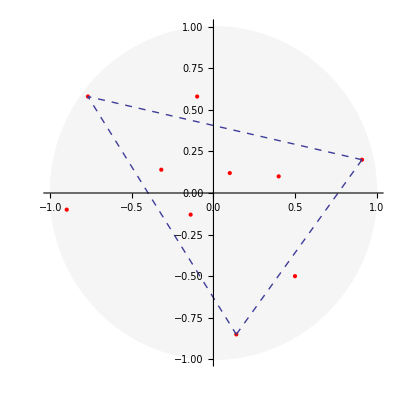

```mathematica
A={{.911,.2},{-.77,.58},{0.14,-.85}};
Show[
 Plot[Sqrt[1-x^2],{x,-1,1},PlotStyle->{GrayLevel[.96]},Filling->Axis,FillingStyle->Directive[GrayLevel[.96],Thickness[.001]]],
Plot[-Sqrt[1-x^2],{x,-1,1},PlotStyle->{GrayLevel[.96]},Filling->Axis,FillingStyle->Directive[GrayLevel[.96],Thickness[.001]]],
ListPlot[pkty,PlotStyle->{Red,PointSize[Small]}],
ListPlot[A,PlotStyle->{Dashed},Joined->True],
ListPlot[{A⟦1⟧,A⟦3⟧},PlotStyle->Directive[{Dashed,PointSize[Medium]}],Joined->True],
AspectRatio->Automatic,PlotRange->All]
```

LOSOWE PUNKTY KULI

```mathematica
λ={.5,.2,.1,.01,.0001};
mm=3;size={3,5,20,50,100};max=4.721075009423214;iter=100;X=pkty;

For[ii=1,ii<=Length[λ],ii++,
For[jj=1,jj<=Length[size],jj++,
wyn={0,0}; it=0;perc=0;
For[q=1,q<=100,q++,
wyn=pbilMDtest[pkty,λ⟦ii⟧,mm,size⟦jj⟧,max,iter];
it+=wyn⟦2⟧;
perc+=wyn⟦1⟧];
out = If[wyn⟦3⟧>max,wyn⟦3⟧,max];
Print["λ = ",λ⟦ii⟧,", size = ",size⟦jj⟧," it = ",it/100.,", % : ",perc,
" (max: ",out,")"];
];
Print["______________________"]
]
```

$Aborted

P: {0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

Maximum = 4.72108 (rzeczywiste = 4.82108) uzyskane po iteracjach: 149 dla punktów:

{{0.911,0.2},{-0.77,0.58},{0.14,-0.85}}

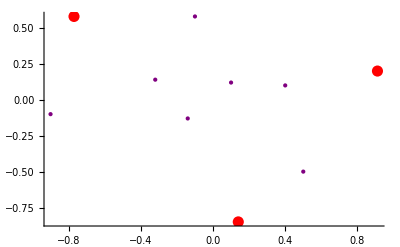

```mathematica
pbilMD[pkty,0.01,3,20,4.821075009423214,150](*spr czy nie ma wiekszego max*)
```

```mathematica
(*Punkty, dla których odległość jest maksymalna *)
wyn={{0.911,0.2},{-0.77,0.58},{0.14,-0.85}};max=∑_(i=1)^2 ∑_(j=i+1)^3 EuclideanDistance[wyn⟦i⟧,wyn⟦j⟧];
```

```mathematica
(*czas*)
λ={.5,.2,.1,.01,.0001};
mm=3;size={3,5,20,50,100};max=4.721075009423214;iter=100;X=pkty;
For[ii=1,ii<=Length[λ],ii++,
For[jj=1,jj<=Length[size],jj++,
d=AbsoluteTime[];
For[q=1,q≤5,q++,
pbilMDtest[X,λ⟦ii⟧,mm,size⟦jj⟧,max,iter];];
Print["λ = ",λ⟦ii⟧,", time :",(AbsoluteTime[DateList[]]-d)/5]
];
Print["______________________"]
]
```

λ = 0.5, time :0.0030002

λ = 0.5, time :0.0052003

λ = 0.5, time :0.0104006

λ = 0.5, time :0.017801

λ = 0.5, time :0.0302017

______________________

λ = 0.2, time :0.0042002

λ = 0.2, time :0.0038002

λ = 0.2, time :0.0100006

λ = 0.2, time :0.018201

λ = 0.2, time :0.0306018

______________________

λ = 0.1, time :0.00780044

λ = 0.1, time :0.0042002

λ = 0.1, time :0.00900052

λ = 0.1, time :0.0194011

λ = 0.1, time :0.0296017

______________________

λ = 0.01, time :0.0024001

λ = 0.01, time :0.0030002

λ = 0.01, time :0.0066004

λ = 0.01, time :0.0130007

λ = 0.01, time :0.0226013

______________________

λ = 0.0001, time :0.0030002

λ = 0.0001, time :0.0026001

λ = 0.0001, time :0.0068004

λ = 0.0001, time :0.0140008

λ = 0.0001, time :0.0260015

______________________

WIERZCHOŁKI SZEŚCIANU

```mathematica
pktyS={{0,0,0},{0,0,1},{0,1,0},{1,0,0},{1,1,0},{1,0,1},{0,1,1},{1,1,1}};
λ={.5,.2,.1,.01,.0001};
mm=2;size={3,5,20,50,100};max=Sqrt[3];iter=100;X=pktyS;
```

```mathematica
For[ii=1,ii<=Length[λ],ii++,
For[jj=1,jj<=Length[size],jj++,
wyn={0,0}; it=0;perc=0;
For[q=1,q≤100,q++,
wyn=pbilMDtest[X,λ⟦ii⟧,mm,size⟦jj⟧,max,iter];
it+=wyn⟦2⟧;
perc+=wyn⟦1⟧];
out = If[wyn⟦3⟧>max,wyn⟦3⟧,max];
Print["λ = ",λ⟦ii⟧,", size = ",size⟦jj⟧," it = ",it/100.,", % : ",perc,
" (max: ",out,")"];
];
Print["______________________"]
]
```

λ = 0.5, size = 3 it = 19.67, % : 83 (max: √3)

λ = 0.5, size = 5 it = 11.52, % : 91 (max: √3)

λ = 0.5, size = 20 it = 1.92, % : 100 (max: √3)

λ = 0.5, size = 50 it = 1.83, % : 100 (max: √3)

λ = 0.5, size = 100 it = 1.87, % : 100 (max: √3)

______________________

λ = 0.2, size = 3 it = 3.78, % : 100 (max: √3)

λ = 0.2, size = 5 it = 2.6, % : 100 (max: √3)

λ = 0.2, size = 20 it = 1.97, % : 100 (max: √3)

λ = 0.2, size = 50 it = 1.81, % : 100 (max: √3)

λ = 0.2, size = 100 it = 1.86, % : 100 (max: √3)

______________________

λ = 0.1, size = 3 it = 3.21, % : 100 (max: √3)

λ = 0.1, size = 5 it = 2.95, % : 100 (max: √3)

λ = 0.1, size = 20 it = 1.86, % : 100 (max: √3)

λ = 0.1, size = 50 it = 1.8, % : 100 (max: √3)

λ = 0.1, size = 100 it = 1.87, % : 100 (max: √3)

______________________

λ = 0.01, size = 3 it = 3.36, % : 100 (max: √3)

λ = 0.01, size = 5 it = 2.71, % : 100 (max: √3)

λ = 0.01, size = 20 it = 1.87, % : 100 (max: √3)

λ = 0.01, size = 50 it = 1.84, % : 100 (max: √3)

λ = 0.01, size = 100 it = 1.81, % : 100 (max: √3)

______________________

λ = 0.0001, size = 3 it = 3.69, % : 100 (max: √3)

λ = 0.0001, size = 5 it = 2.9, % : 100 (max: √3)

λ = 0.0001, size = 20 it = 1.93, % : 100 (max: √3)

λ = 0.0001, size = 50 it = 1.89, % : 100 (max: √3)

λ = 0.0001, size = 100 it = 1.84, % : 100 (max: √3)

______________________

```mathematica
(*Czas*)
pktyS={{0,0,0},{0,0,1},{0,1,0},{1,0,0},{1,1,0},{1,0,1},{0,1,1},{1,1,1}};
λ={.5,.2,.1,.01,.0001};
mm=2;size={3,5,20,50,100};max=Sqrt[3];iter=100;X=pktyS;
For[ii=1,ii<=Length[λ],ii++,
For[jj=1,jj<=Length[size],jj++,
d=AbsoluteTime[];
For[q=1,q≤5,q++,
pbilMDtest[X,λ⟦ii⟧,mm,size⟦jj⟧,max,iter];];
Print["λ = ",λ⟦ii⟧,", time :",(AbsoluteTime[DateList[]]-d)/5]
];
Print["______________________"]
]
```

λ = 0.5, time :0.0022001

λ = 0.5, time :0.0030002

λ = 0.5, time :0.0090005

λ = 0.5, time :0.0156009

λ = 0.5, time :0.0268015

______________________

λ = 0.2, time :0.0022001

λ = 0.2, time :0.0030002

λ = 0.2, time :0.00740042

λ = 0.2, time :0.0154009

λ = 0.2, time :0.0222013

______________________

λ = 0.1, time :0.0018001

λ = 0.1, time :0.0026002

λ = 0.1, time :0.0056003

λ = 0.1, time :0.0122007

λ = 0.1, time :0.0208012

______________________

λ = 0.01, time :0.0016001

λ = 0.01, time :0.0022001

λ = 0.01, time :0.0054003

λ = 0.01, time :0.0108006

λ = 0.01, time :0.0204012

______________________

λ = 0.0001, time :0.0016001

λ = 0.0001, time :0.0026001

λ = 0.0001, time :0.0050003

λ = 0.0001, time :0.0108006

λ = 0.0001, time :0.0136008

______________________